## ^187Au Fitting the negative parity bands

```mathematica
ClearAll["Global*`"]
```

### Analytical formulae

```mathematica
I0=4.5;
j=5.5;
IF[MOI_]:=1/(2*MOI);
RAD[angle_]:=angle*π/180;
HMin[I_,j_,A1_,A2_,A3_,V_,γ_]:=(A2+A3)(I+j)/2+A1*(I-j)^2-V*(2j-1)/(j+1)*Sin[γ+π/6];
B1[I_,j_,A1_,A2_,A3_,V_,γ_]:=-1*(((2I-1)*(A3-A1)+2j*A1)*((2I-1)*(A2-A1)+2j*A1)+8*A2*A3*I*j+((2j-1)(A3-A1)+2I*A1+V*(2j-1)/(j(j+1))Sqrt[3](Sqrt[3]Cos[γ]+Sin[γ]))*((2j-1)(A2-A1)+2I*A1+V*(2j-1)/(j(j+1))2Sqrt[3]Sin[γ]));
C1[I_,j_,A1_,A2_,A3_,V_,γ_]:=((((2I-1)(A3-A1)+2j*A1)*((2j-1)(A3-A1)+2I*A1+V*(2j-1)/(j(j+1))Sqrt[3](Sqrt[3]Cos[γ]+Sin[γ]))-4I*j*A3^2)*(((2I-1)*(A2-A1)+2j*A1)*((2j-1)(A2-A1)+2I*A1+V*(2j-1)/(j(j+1))2Sqrt[3]Sin[γ])-4I*j*A2^2));
Omega1[I_,j_,A1_,A2_,A3_,V_,γ_]:=Sqrt[1/2(-B1[I,j,A1,A2,A3,V,γ]-Sqrt[B1[I,j,A1,A2,A3,V,γ]^2-4*C1[I,j,A1,A2,A3,V,γ]])];
Omega2[I_,j_,A1_,A2_,A3_,V_,γ_]:=Sqrt[1/2(-B1[I,j,A1,A2,A3,V,γ]+Sqrt[B1[I,j,A1,A2,A3,V,γ]^2-4*C1[I,j,A1,A2,A3,V,γ]])];
Energy[nw1_,nw2_,I_,j_,A1_,A2_,A3_,V_,γ_]:=HMin[I,j,A1,A2,A3,V,γ]+Omega1[I,j,A1,A2,A3,V,γ](nw1+1/2)+Omega2[I,j,A1,A2,A3,V,γ](nw2+1/2);
ExcEn[nw1_,nw2_,I_,A1_,A2_,A3_,V_,γ_]:=Energy[nw1,nw2,I,j,A1,A2,A3,V,γ]-Energy[0,0,I0,j,A1,A2,A3,V,γ];
band1[I_,I1_,I2_,I3_,V_,γ_]:=ExcEn[0,0,I,IF[I1],IF[I2],IF[I3],V,RAD[γ]];
band2[I_,I1_,I2_,I3_,V_,γ_]:=ExcEn[1,0,I,IF[I1],IF[I2],IF[I3],V,RAD[γ]];
```

#### Experimental data

```mathematica
spin1=Table[N[i],{i,9/2,45/2,2}];
spin2=Table[N[i],{i,11/2,31/2,2}];
yrast=Reverse[N[{5036.5,4259.6,3502.0,2796.2,2158.4,1591.2,1100.3,687.0,353.3,120.5}/1000]];
tw1=Reverse[N[{3013.7,2354.7,1739.3,1231.7,815.2,496.5}/1000]];
bandHead=yrast[[1]];
yrast=Table[yrast[[i]]-bandHead,{i,1,Length[yrast]}];
tw1=Table[tw1[[i]]-bandHead,{i,1,Length[tw1]}];
```

### Fitting procedure

#### Bounds

```mathematica
i1bounds={40,80};
i2bounds={1,30};
i3bounds={5,50};
vbounds={0.01,5.0};
gmbounds={20,25};
```

#### Minimization function

```mathematica
chi2[I1_,I2_,I3_,V_,γ_]:=If[Im[Sqrt[1/(Length[spin1]+Length[spin2]+1)(Sum[(yrast[[i]]-band1[spin1[[i]],I1,I2,I3,V,γ])^2,{i,1,Length[spin1]}]+Sum[(tw1[[i]]-band2[spin2[[i]],I1,I2,I3,V,γ])^2,{i,1,Length[spin2]}])]]==0,Sqrt[1/(Length[spin1]+Length[spin2]+1)(Sum[(yrast[[i]]-band1[spin1[[i]],I1,I2,I3,V,γ])^2,{i,1,Length[spin1]}]+Sum[(tw1[[i]]-band2[spin2[[i]],I1,I2,I3,V,γ])^2,{i,1,Length[spin2]}])],10^9];
min=NMinimize[{chi2[I1,I2,I3,V,γ],i1bounds[[1]]≤I1≤i1bounds[[2]]&&i2bounds[[1]]≤I2≤i2bounds[[2]]&&i3bounds[[1]]≤I3≤i3bounds[[2]]&&vbounds[[1]]≤V≤vbounds[[2]]&&gmbounds[[1]]≤γ≤gmbounds[[2]]},{I1,I2,I3,V,γ}];
params=Values@min[[2]];
rms=min[[1]];
Print["RMS-> ",rms,"\nP -> ",params]
```

RMS-> 0.0234376
P -> {55.108,3.81622,19.564,2.01901,20.}

## Plot data

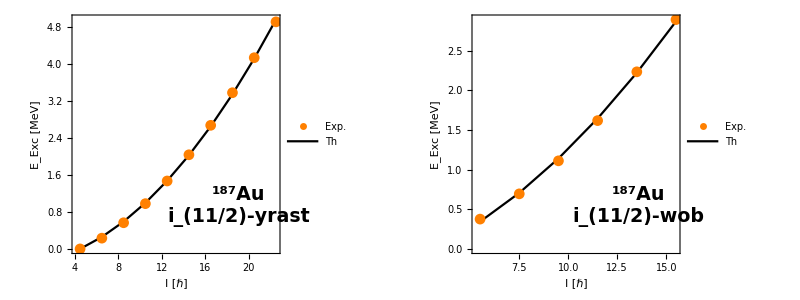

```mathematica
label1="^187Au\ni_(11/2)-yrast";
label2="^187Au\ni_(11/2)-wob";
plotFunction[band_,params_,spins_,expData_,label_]:=ListPlot[{Table[{spins[[i]],expData[[i]]},{i,1,Length[spins]}],Table[{spins[[i]],band[spins[[i]],params[[1]],params[[2]],params[[3]],params[[4]],params[[5]]]},{i,1,Length[spins]}]},Frame->True,Axes->False,AspectRatio->0.8,FrameLabel->{"I [ℏ]","E_Exc [MeV]"},PlotLegends->Placed[{"Exp.","Th"},{0.25,0.75}],FrameStyle->Directive[Thick,Black],LabelStyle->{19,Black,Bold,FontFamily->"Times"},Joined->{False, True},PlotStyle->{Orange,Black},PlotMarkers->{{Automatic,11},None},Epilog->Inset[Style[label,19,Black,Bold,FontFamily->"Times"],Scaled[{0.8,0.2}]],PlotRange->Full];
plot1=plotFunction[band1,params,spin1,yrast,label1];
plot2=plotFunction[band2,params,spin2,tw1,label2];
Grid[{{Show[plot1,ImageSize->Medium],Show[plot2,ImageSize->Medium]}},Frame->All]
(*Export the plots to files*)
Export["/Users/robertpoenaru/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/183-187Au_Wobbling-Bands/src/python/app/assets/plots/Au_187_1.pdf",Show[plot1],ImageResolution->1200];
Export["/Users/robertpoenaru/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DFT/183-187Au_Wobbling-Bands/src/python/app/assets/plots/Au_187_2.pdf",Show[plot2],ImageResolution->1200];
```

## Printer function

```mathematica
printer[params_,spins_,expdata_,modelband_]:=Do[Print[spins[[i]]," ",expdata[[i]]," ",modelband[spins[[i]],params[[1]],params[[2]],params[[3]],params[[4]],params[[5]]]],{i,1,Length[spins]}];tabular[params_,spins_,expdata_,modelband_]:=Table[{spins[[i]],expdata[[i]],modelband[spins[[i]],params[[1]],params[[2]],params[[3]],params[[4]],params[[5]]]},{i,1,Length[spins]}];
grider[title_,rms_,params_,spins_,expdata_,modelband_]:=Grid[{{title},{StringTemplate["RMS = ``"][rms]},{StringTemplate["P=I1=`` I2=`` I3=``\nV=`` gm=``"][params[[1]],params[[2]],params[[3]],params[[4]],params[[5]]]},{Grid[tabular[params,spins,expdata,modelband]]}},ItemStyle->{14,Black},FrameStyle->Directive[Black,Thick],Frame->All,Background->{None,{Green}}];
```

```mathematica
pp=params;
grider["Band-1 ; j=i_(11/2)",chi2[pp[[1]],pp[[2]],pp[[3]],pp[[4]],pp[[5]]],pp,spin1,yrast,band1]
grider["Band-2 ; j=i_(11/2)",chi2[pp[[1]],pp[[2]],pp[[3]],pp[[4]],pp[[5]]],pp,spin2,tw1,band2]
```

Band-1 ; j=i_(11/2)
RMS = 0.0234376
P=I1=55.108 I2=3.81622 I3=19.564
V=2.01901 gm=20.0
4.5 | 0. | 0.
6.5 | 0.2328 | 0.258541
8.5 | 0.5665 | 0.590571
10.5 | 0.9798 | 0.996048
12.5 | 1.4707 | 1.47484
14.5 | 2.0379 | 2.02682
16.5 | 2.6757 | 2.65188
18.5 | 3.3815 | 3.34992
20.5 | 4.1391 | 4.12088
22.5 | 4.916 | 4.9647

Band-2 ; j=i_(11/2)
RMS = 0.0234376
P=I1=55.108 I2=3.81622 I3=19.564
V=2.01901 gm=20.0
5.5 | 0.376 | 0.343785
7.5 | 0.6947 | 0.706516
9.5 | 1.1112 | 1.14038
11.5 | 1.6188 | 1.64558
13.5 | 2.2342 | 2.22215
15.5 | 2.8932 | 2.87011